真实世界的数据

Wolfram 语言的一个核心特征是，它内置了大量的真实世界数据。它有关于国家、动物和电影的数据，等等。它从 Wolfram 知识库中获取所有这些数据，该知识库一直在更新，它是 Wolfram|Alpha 和基于它的服务的动力。

但是，你如何在 Wolfram 语言中谈论一个国家呢？最简单的方法就是使用普通英语。你可以通过按下ctrl= (按住 Control 键并按下 = 键)，或者在触摸设备上按下  按钮，来告诉 Wolfram 语言你要给它提供普通英语。

```mathematica
LinguisticAssistant
```

输入普通英语“united states”：

```mathematica
LinguisticAssistant
```

一旦你按下return (或点击其它地方)，Wolfram 语言将尝试解析你输入的内容。如果它成功了，它就会显示一个小黄框，表示一个 Wolfram 语言实体。在本例中，它是对应于美国的实体。

```mathematica
LinguisticAssistant
```

点击复选标记，确认这是你想要的：

```mathematica
Entity["Country","UnitedStates"]
```

现在你可以查询这个实体的很多属性。比如你可以查询美国国旗。

查询美国的国旗属性：



```mathematica
Entity["Country","UnitedStates"]["Flag"]
```

你可以继续用你得到的结果进行计算，比如这里可以进行图像处理。

对美国国旗进行反色：

```mathematica
ColorNegate[-Graphics-]
```

-Graphics-

如果你只想得到美国国旗，你可以直接用英语来查询它：

```mathematica
LinguisticAssistant
```

-Graphics-

EntityValue 是用来查询属性值的一种更灵活的方式。

使用 EntityValue 来获取美国国旗：

```mathematica
EntityValue[Entity["Country","UnitedStates"],"Flag"]
```

-Graphics-

EntityValue 也可以用于实体的列表。

获取一系列国家的国旗：

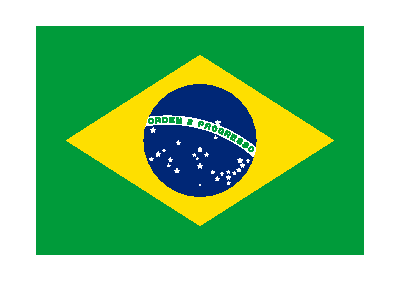

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityValue[{Entity["Country","UnitedStates"],Entity["Country","Brazil"],Entity["Country","China"]},"Flag"]
```

Wolfram 语言对国家有很深的了解，就像对许多其他事物一样。

找出列表中的国家中有多少个广播电台：

```mathematica
EntityValue[{Entity["Country","UnitedStates"],Entity["Country","Brazil"],Entity["Country","China"]},"RadioStations"]
```

{13769,1822,673}

将结果做成饼状图：

```mathematica
PieChart[EntityValue[{Entity["Country","UnitedStates"],Entity["Country","Brazil"],Entity["Country","China"]},"RadioStations"]]
```

-Graphics-

寻找与瑞士接壤的国家：

```mathematica
Entity["Country","Switzerland"]["BorderingCountries"]
```

{Austria,France,Germany,Italy,Liechtenstein}

查询它们的国旗：

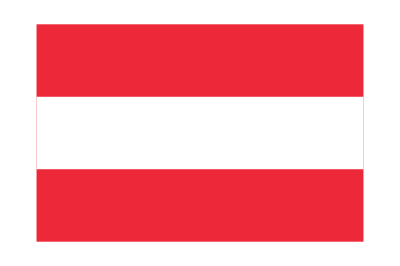


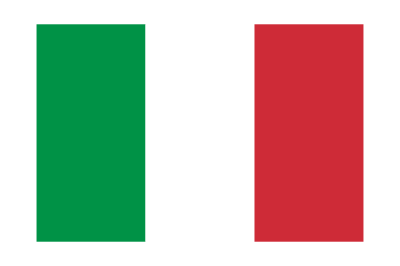
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityValue[Entity["Country","Switzerland"]["BorderingCountries"],"Flag"]
```

有时你会想查看一类实体，比如说，行星。

查询行星，并得到与行星对应的实体类：

```mathematica
LinguisticAssistant
```

planets

实体类用  表示。你可以使用 EntityList 来获得一个类中所有实体的列表。

获取行星的列表：

```mathematica
EntityList[EntityClass["Planet",All]]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

获取所有行星的图像：

```mathematica
EntityValue[EntityClass["Planet",All],"Image"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

EntityValue 实际上可以直接处理实体类，所以你不需要先用 EntityList。

获取每颗行星的半径，并将其制成柱状图：

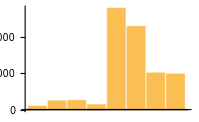

```mathematica
BarChart[EntityValue[EntityClass["Planet",All],"Radius"]]
```

使用普通英语来描述事物是非常方便的。但缺点是，它可能会有歧义。如果你说“mercury”，你是指水星还是指化学元素汞，还是指其他叫“mercury”的东西？当你使用ctrl= 时，它总是做出一个初始选择。但如果你点击 ，你就可以更改为另一选择。点击  来接受选择。

```mathematica
LinguisticAssistant
```

要了解 Wolfram 语言在内部如何表示实体，你可以使用 InputForm。

显示表示美国的实体的内部形式：

```mathematica
InputForm[LinguisticAssistant]
```

Entity["Country", "UnitedStates"]

显示纽约市的内部形式：

```mathematica
InputForm[LinguisticAssistant]
```

Entity["City", {"NewYork", "NewYork", "UnitedStates"}]

Wolfram 语言中有数百万个实体，每个实体都有明确的内部形式。原则上，你可以使用任何实体的内部形式输入。但除非你重复使用同一个实体，否则使用ctrl= 并以普通英语来输入实体的名字会更实用。

Wolfram 语言中有数千种不同类型的实体，涵盖了各种各样的知识领域。要了解这些实体，请查阅 Wolfram 语言文档，或者 Wolfram|Alpha 实例页面。每种类型的实体都有一系列属性，通常有数百个。找到这些属性的其中一种方法是使用 EntityProperties。

游乐园的可能属性：

```mathematica
EntityProperties["AmusementPark"]
```

{administrative division,type,area,city,closing date,country,image,latitude,longitude,name,number of rides,opening date,owner,coordinates,slogan,rides,status}

不过在实践中，一个好的方法是用普通的英语询问某个实体的属性，然后看看找到的解释，并重新使用其中的属性。

询问埃菲尔铁塔的高度：

```mathematica
LinguisticAssistant
```

```mathematica
LinguisticAssistant
```

1062.99 ft

重用"Height"属性，并将其应用到大金字塔上：

```mathematica
Entity["Building","GreatPyramidOfGiza::jbm66"]["Height"]
```

456.037 ft

不同类型的实体有不同的属性。许多类型的实体都有一个共同属性是"Image"。

获取各种实体的图像：

```mathematica
Entity["Species","Species:PhascolarctosCinereus"]["Image"]
```

-Graphics-

```mathematica
Entity["Building","EiffelTower::5h9w8"]["Image"]
```

-Graphics-

```mathematica
Entity["Artwork","TheStarryNight::VincentVanGogh"]["Image"]
```

-Graphics-

```mathematica
Entity["Person","StephenWolfram::j276d"]["Image"]
```

-Graphics-

其他类型的对象有其他属性：

咖啡因分子的示意图：

```mathematica
Entity["Chemical","Caffeine"]["MoleculePlot"]
```

-Graphics-

可旋转的骷髅头的三维图形：

```mathematica
Entity["AnatomicalStructure","Skull"]["Graphics3D"]
```

-Graphics-

一个可以折叠成我们公司3D 标志的网格：

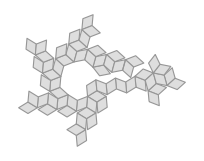

```mathematica
Entity["Polyhedron","RhombicHexecontahedron"]["NetImage"]
```

词汇

ctrl=   |   | 使用普通英语输入
EntityList[class] |   | 类型中的实体
EntityValue[entities,property] |   | 实体的属性值
EntityProperties[type] |   | 实体类型的属性列表
InputForm[entity] |   | 实体在 Wolfram 语言中的内部表示

"共有 13 道习题"
"以及 3 道附加题" | "开始练习 »"

找到瑞士(Switzerland)的国旗。»

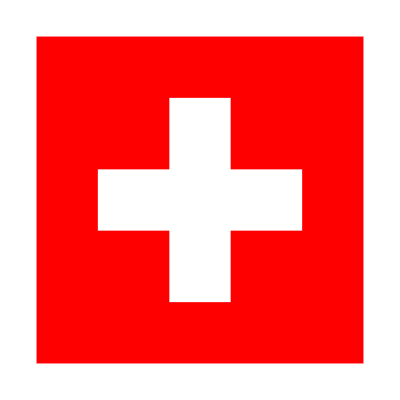
| 期望输出： |  
  | -Graphics- |

获得一个大象的图像。»

| 期望输出示例： |  
  | -Graphics- |

使用 "Mass" 属性来生成一个行星质量的列表。»

| 期望输出： |  
  | {3.30104×10^23 "kg",4.86732×10^24 "kg",5.9721986×10^24 "kg",6.41693×10^23 "kg",1.89813×10^27 "kg",5.68319×10^26 "kg",8.68103×10^25 "kg",1.0241×10^26 "kg"} |

创建一个行星质量的条形图。»

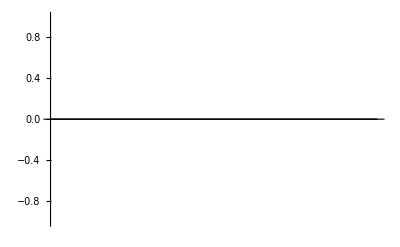
| 期望输出： |  
  | -Graphics- |

将行星的图像拼贴在一起。»

| 期望输出： |  
  | -Graphics- |

对中国的国旗进行边缘检测。»

| 期望输出： |  
  | -Graphics- |

找到帝国大厦(Empire State Building)的高度。»

| 期望输出： |  
  | 1250. "ft" |

计算帝国大厦的高度除以大金字塔( Great Pyramid)的高度。»

| 期望输出： |  
  | 2.74101 |

计算珠穆朗玛峰(Mount Everest)的海拔高度除以帝国大厦的高度。»

| 期望输出： |  
  | 23.2231 |

找出《星空》(Starry Night)这幅画中的主色调。»

| 期望输出： |  
  | {RGBColor[0.2768655066668183, 0.3712643071964756, 0.5642037010622294],RGBColor[0.12012834022024377, 0.13444662562587364, 0.12819278684469784],RGBColor[0.589686385011058, 0.6392285324724452, 0.5548502694119095]} |

创建欧洲(Europe)所有国家的国旗的拼贴图片，然后找出其中的主色。»

| 期望输出： |  
  | {RGBColor[0.8384380770968652, 0.10378446717897716, 0.18712551720692133],RGBColor[0.9930488857973235, 0.9885807188350121, 0.988462260402767],RGBColor[0.07144901267884562, 0.24438683922410798, 0.587652291734621],RGBColor[0.9744416667249923, 0.8004261361448077, 0.09438578646953585],RGBColor[0.1269646589300012, 0.5321736217747745, 0.2846829216683256]} |

将欧洲各国的 GDP 创建为饼图。»

| 期望输出： |  
  | -Graphics- |

将考拉(koala)的图像与澳大利亚(Australian)国旗的图像进行相加。»

| 期望输出示例： |  
  | -Graphics- |

使用“FlagImage”属性，将欧洲所有国家的国旗制作成图像拼贴画。»

| 期望输出： |  
  | -Graphics- |

对画作《星空》的图像进行边缘检测。»

| 期望输出： |  
  | -Graphics- |

计算画作《蒙娜丽莎》的负片。»

| 期望输出： |  
  | -Graphics- |

问&答

Wolfram 语言从哪里获取其真实世界的数据？

这一切都来自于核心 Wolfram 知识库。多年来，我们一直在建立这个知识库，从成千上万的主要来源中精心策划数据。

Wolfram 语言中的数据是否定期更新？

是的。我们花了很多精力来使之保持最新。事实上，每秒钟都有关于股市价格、天气、地震、飞机位置等新数据流入。

Wolfram 语言中的数据有多精确？

我们花了很多功夫使其尽可能准确，并进行了广泛的检查。但最终我们往往需要依赖政府和其他外部组织的报告。

与 Wolfram|Alpha 的关系是什么？

Wolfram|Alpha 使用与 Wolfram 语言相同的知识库。

我该如何查阅一个特定的实体？

不管你想怎么做。Wolfram 语言设置为能理解所有常见的实体查询方式。(“New York City”, “NYC”, “the big apple”等等，都可以。)

我怎样才能找到一个给定实体的所有属性和值？

使用 entity["Dataset"] 或者 entity["PropertyAssociation"]。

如果 EntityValue 给出了 Missing[...]，是什么意思？

这表示尚不知道你所要求的值，或者至少不在 Wolfram 知识库中。使用 DeleteMissing 来删除列表中的 Missing[...]元素。

我可以建立我自己的实体，并放入我自己的相关数据吗？

可以，使用 EntityStore。

技术笔记

Wolfram 知识库存储在云端，所以即使你使用的是 Wolfram 语言的桌面版本，你也需要连接到网络上才能获得真实世界的数据。

Wolfram 知识库中包含了数万亿的具体事实和值，使用各种底层数据库技术存储在 Wolfram 语言的符号框架中。

Wolfram 知识库是由大量的原始数据源来系统地建立和策划的，它并不是来自于网络搜索。

现实世界的数据往往涉及单位，我们将在下一章中讨论。

你可以不使用自然语言，而是通过特定的函数如 CountryData 和 MovieData 来访问 Wolfram 知识库，有时这可能会更快。

如果您想找到某项数据的原始来源，您可以查看文档(例如 CountryData 等)，或者您可以在 Wolfram|Alpha 中查询数据，并跟踪源链接。

有时你想谈论一个实体的特殊实例，如某个特定年份中的国家，或特定数量的物质。你可以使用 EntityInstance 来完成这个。

RandomEntity 用于查找给定类型的随机实体。

实体和属性之间有一个对称性。entity[property] 给出的结果与 property[entity] 相同。 要获得多个属性的值，使用 entity[{p_1,p_2,...}]；要获得多个实体的值，使用 property[{e_1,e_2,...}]。(注意，对于 property[entity]，你需要完整的属性对象，就像从 ctrl= 获得的那样，而不仅仅是作为字符串的属性名称)。

探索更多

Wolfram 知识库主要涵盖的领域 »

地理数据与计算 »

科学和医学的数据与计算 »

工程数据与计算 »

社会、文化与语言数据 »